```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_]:=(
data=Apply[ds,directive];
Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,3}]
)
```

```mathematica
getPlotM[M_,L_]:=(
SetOptions[LinTicks,TickLengthScale->1.5];

plt=ListPlot[M,
DataRange->{{0-1/L,2+1/L},{-3,7}},ImageSize->Medium,
Joined->True,
PlotMarkers->Automatic,
Frame->True,Axes->False,
FrameStyle->Directive[Black,20,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,12],
PlotRange->{{0,2},{-0.5,3.0}},
PlotLegends->Placed[Automatic,Right],
ClippingStyle->Automatic,
AspectRatio->0.75,
FrameLabel->{"k / π","∫A(k,ω)ω^ndω"},
Epilog->Text[
Style[StringJoin["J = ",ToString[NumberForm[J,{3,1}]],"t,\nλ = ",ToString[NumberForm[B,{3,1}]]],Black,16,FontFamily->"Bookman Old Style"],
{1.0,2.7}],
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}}
];

plt
)
```

```mathematica
getNthMoment[spc_,n_]:=(
k=spc[[1]];
ωnth=If[n==0,1,(spc[[2]])^n];
dω=(ω[[-1]]-ω[[1]])/(Length[ω]-1);
A=spc[[3]];
M=Table[0,Length[k]];
For[it=1,it≤Length[k],it++,
M[[it]]={k[[it]],Total[A[[it,;;]]ωnth]dω}
];
M
)
```

```mathematica
makePlotsM[n_]:=(
dirc={Select[#coupling==J&&#size==L&&#interaction==B&]};
keys={"momentum","energy","spectrum"};

plots={};
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys];
AppendTo[buff,getPlotM[getNthMoment[spc,n],L]];
),{B,spcAvail["interaction"]//Normal}];
AppendTo[plots,buff];
),{L,spcAvail["size"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"28-2-28_-1.0-1.0-1.0"};
head = "spc";
MPlots={};
For[n=0,n<3,n++,(
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[MPlots,makePlotsM[n]];
),{tail,tails}]
)]
```

```mathematica
spcAvail
```

Dataset[<>]

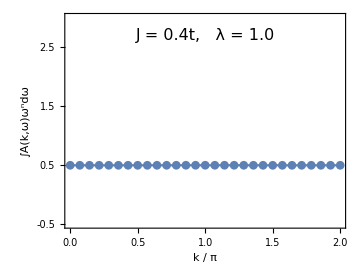
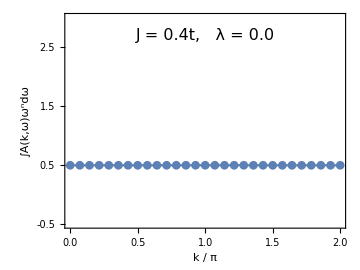
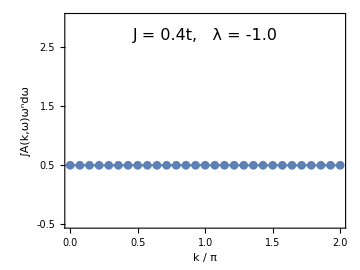
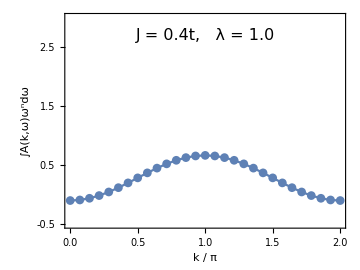
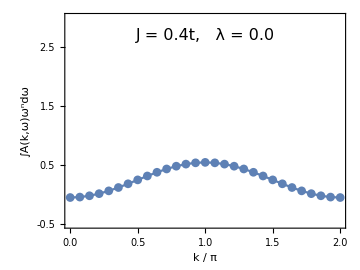
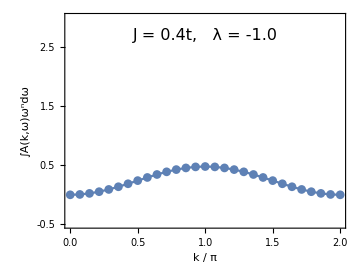
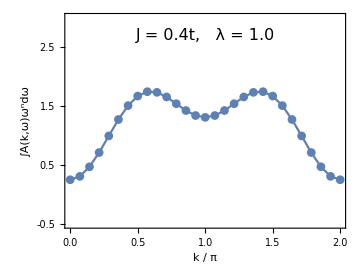
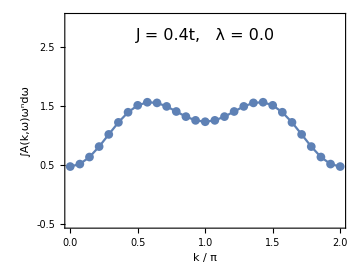

```mathematica
Grid[Reverse[MPlots[[;;]],3]]
```

```mathematica
restylePlot[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]]
```

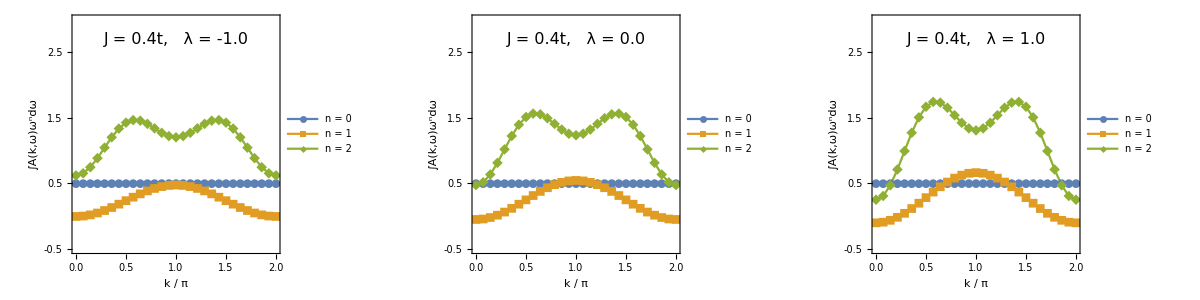

```mathematica
colors=ColorData[];
legend=Table[StringJoin["n = ",ToString[i]],{i,0,3}];
MPlotsJoined={Table[restylePlot[Show[MPlots[[;;,1,i]]],PlotStyle->colors,PlotLegends->Placed[legend,{0.85,0.8}],PlotMarkers->Automatic],{i,3}]};
Grid[MPlotsJoined]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/","moments","/",
"nm","_L=",ToString[spcAvail["size"][[iN]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,MPlotsJoined[[iN,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
SavePlots[]
```